# PeterBurbery/MixedGraphs

A collection of mixed graph functionality

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"Guides"

"MixedGraphFunctions.nb"Documentation/English/Guides/MixedGraphFunctions.nb

"ReferencePages"

"Symbols"

"BlossonInequalities.nb"Documentation/English/ReferencePages/Symbols/BlossonInequalities.nb

"EulerizeGraph.nb"Documentation/English/ReferencePages/Symbols/EulerizeGraph.nb

"GeneralizedGraphData.nb"Documentation/English/ReferencePages/Symbols/GeneralizedGraphData.nb

"GraphConvexHull.nb"Documentation/English/ReferencePages/Symbols/GraphConvexHull.nb

"GraphicalDegreeSequenceQ.nb"Documentation/English/ReferencePages/Symbols/GraphicalDegreeSequenceQ.nb

"GraphInformation.nb"Documentation/English/ReferencePages/Symbols/GraphInformation.nb

"MixedGraphDirectedArcs.nb"Documentation/English/ReferencePages/Symbols/MixedGraphDirectedArcs.nb

"MixedGraphToDigraph.nb"Documentation/English/ReferencePages/Symbols/MixedGraphToDigraph.nb

"MixedGraphUndirectedEdges.nb"Documentation/English/ReferencePages/Symbols/MixedGraphUndirectedEdges.nb

"OddNodes.nb"Documentation/English/ReferencePages/Symbols/OddNodes.nb

"RandomCustomGraph - Copy.nb"Documentation/English/ReferencePages/Symbols/RandomCustomGraph - Copy.nb

"RandomCustomGraph.nb"Documentation/English/ReferencePages/Symbols/RandomCustomGraph.nb

"RandomMixedGraph.nb"Documentation/English/ReferencePages/Symbols/RandomMixedGraph.nb

"RandomSymbolicMixedGraph.nb"Documentation/English/ReferencePages/Symbols/RandomSymbolicMixedGraph.nb

"RandomSymbolicWeightedMixedGraph.nb"Documentation/English/ReferencePages/Symbols/RandomSymbolicWeightedMixedGraph.nb

"RandomWeightedMixedGraph.nb"Documentation/English/ReferencePages/Symbols/RandomWeightedMixedGraph.nb

"ResistanceMatrix.nb"Documentation/English/ReferencePages/Symbols/ResistanceMatrix.nb

"TakeLargestGraphComponentBy.nb"Documentation/English/ReferencePages/Symbols/TakeLargestGraphComponentBy.nb

"UndirectedGraphToMixedGraph.nb"Documentation/English/ReferencePages/Symbols/UndirectedGraphToMixedGraph.nb

"Tutorials"

"Kernel"

"MixedGraphs.wl"Kernel/MixedGraphs.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

This paclet contains a functions for manipulating, generating, and analyzing mixed graphs.

### Details

this is part of a Wolfram Summer School 2022 project

### Main Guide Page

"Documentation/English/Guides/MixedGraphFunctions.nb"

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[]
```

{C:\Users\peter\Documents\GitHub\MixedGraphPaclet\Mixed Graphs}

```mathematica
Block[{$ContextPath},Get[]]
```

### Basic Examples

Generate a random mixed graph with 20 vertices and 54 edges with 0.75 directed edges:

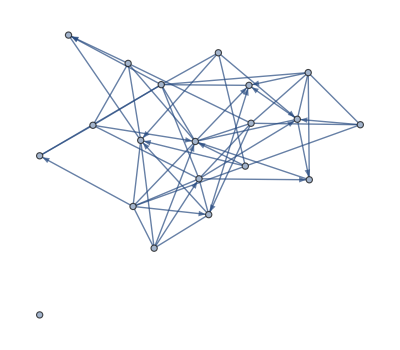

```mathematica
RandomMixedGraph[{20,54},0.75]
```

Create a list of 3 random mixed graphs with 20 vertices and 54 edges:

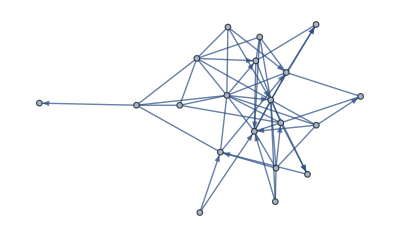
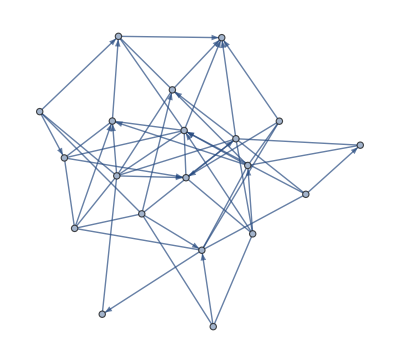
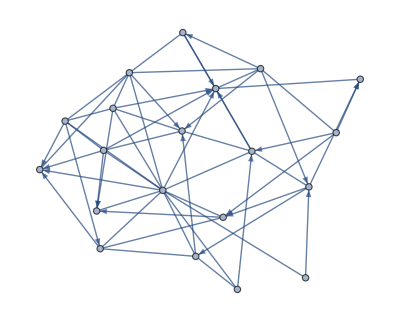

```mathematica
RandomMixedGraph[{20,54},.75,3]
```

Create a random mixed graph from a graph distribution:

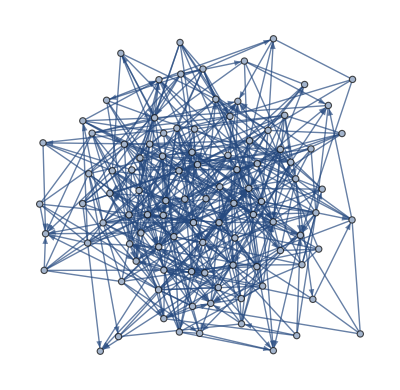

```mathematica
RandomMixedGraph[BernoulliGraphDistribution[100,0.1],0.75]
```

Create a list of 3 random mixed graphs with a graph distribution:

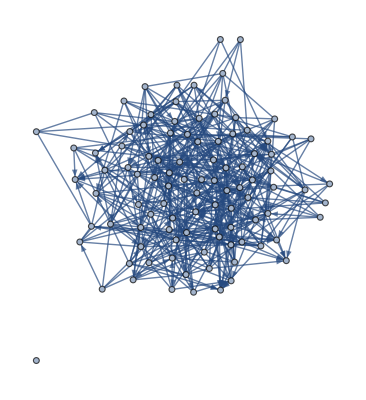
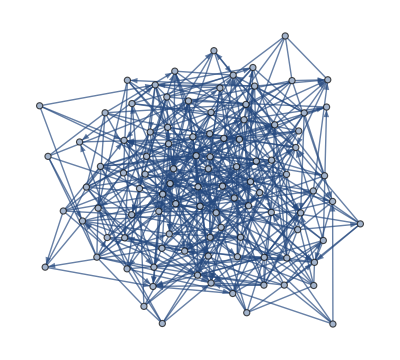
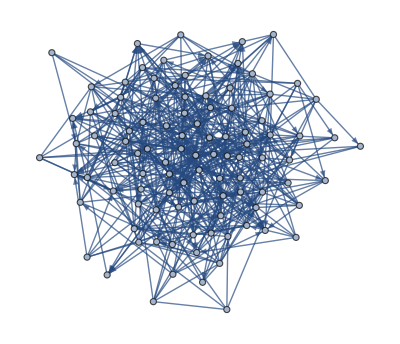

```mathematica
RandomMixedGraph[BernoulliGraphDistribution[100,0.1],0.75,3]
```

### Scope

Create a random mixed graph with the Barabasi-Albert graph distribution:

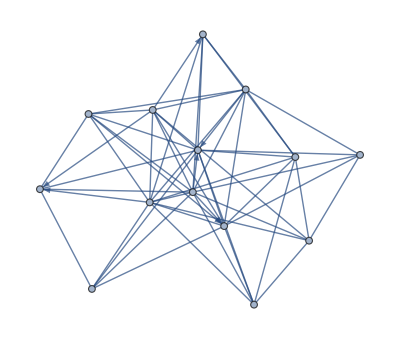

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[14,5],.2]
```

Create a list of mixed graphs:

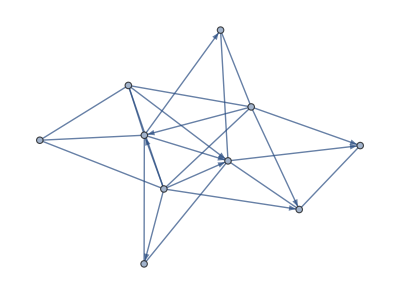
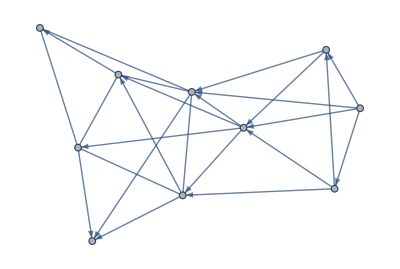
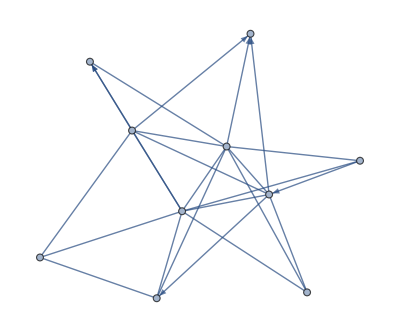
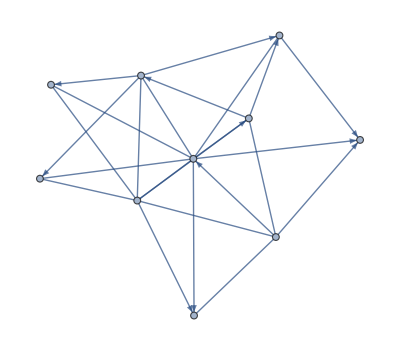

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[10,3],.75,4]
```

Create a mixed graph with the degree graph vertex distribution:

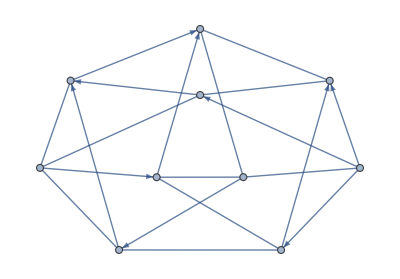

```mathematica
RandomMixedGraph[DegreeGraphDistribution[{4,4,4,4,4,4,4,4,4,4}],.5]
```

Create a mixed graph with the price graph distribution based on an attractiveness parameter of 1:

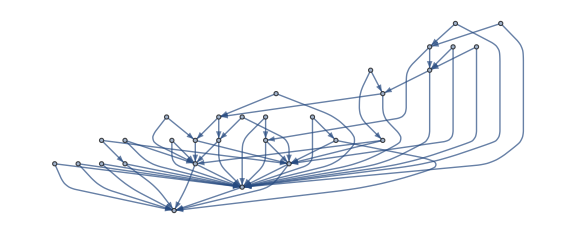

```mathematica
RandomMixedGraph[PriceGraphDistribution[30,2,1],.75,ImageSize->Large]
```

Create a random mixed graph that obeys a spatial graph distribution:

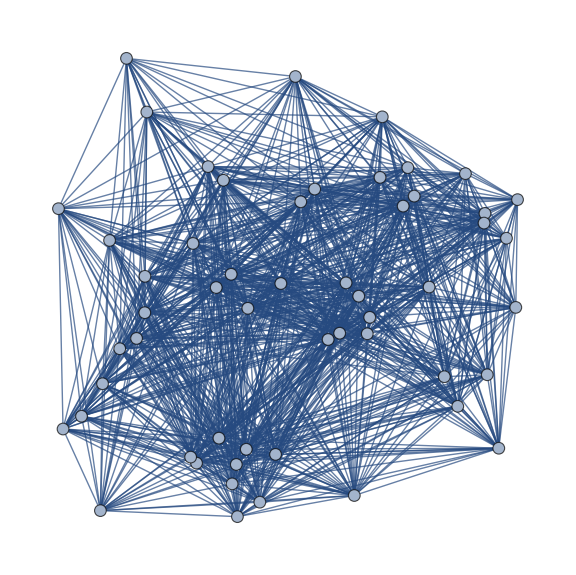

```mathematica
RandomMixedGraph[SpatialGraphDistribution[54,2/3],.7,ImageSize->Large]
```

Use the uniform graph distribution for a mixed graph:

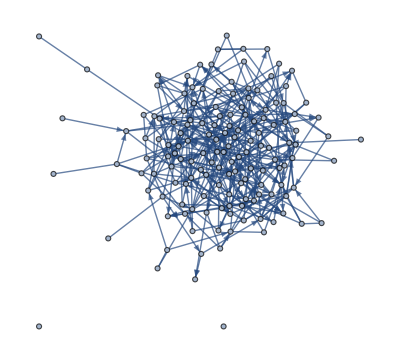

```mathematica
RandomMixedGraph[UniformGraphDistribution[148,403],.7]
```

Create a random mixed graph generated with the Watts–Strogatz graph distribution:

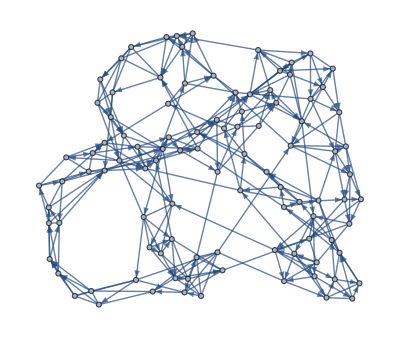

```mathematica
RandomMixedGraph[WattsStrogatzGraphDistribution[100,0.1,3],.6]
```

Create a list of mixed graphs:

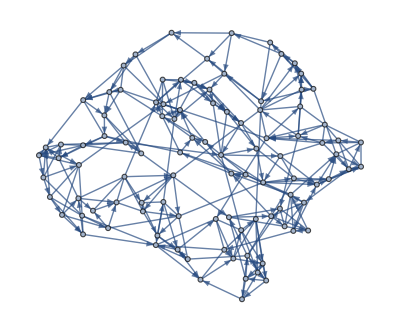
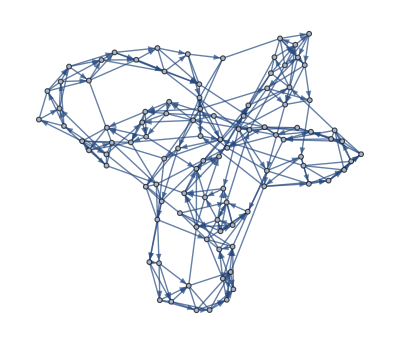
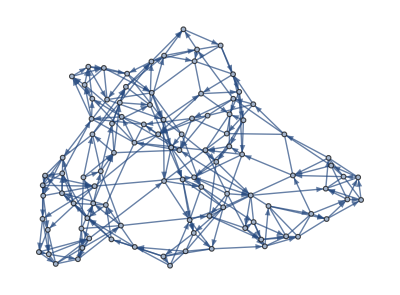

```mathematica
RandomMixedGraph[WattsStrogatzGraphDistribution[100,0.1,3],.6,3]
```

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/mixed-graphs-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Graph theory

mixed graph

Arc routing

Mixed Chinese Postman MCP

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

EulerizeGraph

UndirectedGraphToMixedGraph

OrientedGraphQ

PerfectGraphQ

### Source/Reference Citation

Arc Routing: Problems, Methods and Applications by Ángel Corberán and Gilbert Laporte

### Links

Arc routing—Wikipedia

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies <+$Path+>, <+Directory+>, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public <+ResourceObject+> content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of <+SystemCredential+>Click for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via <+ExternalEvaluate+>
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

I am using this for a Wolfram Summer School 2022 project.

DocumentationBuild`Info`GetNotebookHistoryData::notfound: Could not find the history data for Excised

General::stop: Further output of DocumentationBuild`Info`GetNotebookHistoryData::notfound will be suppressed during this calculation.

DocumentationBuild`Info`GetNotebookHistoryData::notfound: Could not find the history data for Excised

DeleteFile::ioarg: I/O operation is not valid for C:\Users\peter\AppData\Roaming\Mathematica\SystemFiles\FrontEnd\StyleSheets\Wolfram\Reference.nb.